# Functional form harvest output vs preciptation

```mathematica
ClearAll[x,a,b,y]
```

## Coefficient functions

x0 = shifts the function across the x axis
L = superior asymptote
k = steepness of the curve

#### Coefficient “a”

```mathematica
ClearAll[L,x0,k,a,b,y, x]
```

```mathematica
La=200
```

200

```mathematica
k=0.005
```

0.005

```mathematica
x0 = 800
```

800

```mathematica
a = 0.129*z* Exp[-0.0009z]
```

0.129 ⅇ^(-0.0009 z) z

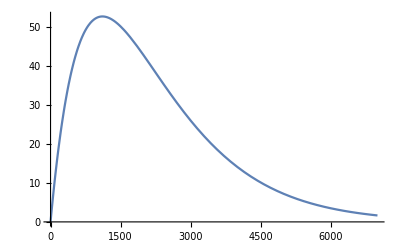

```mathematica
Plot[a,{z,0.,7000.}]
```

#### Coefficient “b”

```mathematica
b = Lb/(1+Exp[-kb(z-x0b)])
```

Lb/(1+ⅇ^(-kb (-x0b+z)))

```mathematica
b=-68.7/(1+ⅇ^(-2 (-2+z)))+89.8
```

89.8-68.7/(1+ⅇ^(-2 (-2+z)))

```mathematica
Manipulate[Plot[Lb/(1+ⅇ^(-kb (-x0b+z)))+e,{z,0,10}, PlotRange->{{0,10},{0,100}}],{Lb,-100,0},{kb,0.01,2},{x0b,0,30},{e,0,200}]
```

#### Where z is precipitation

## Harvest Output function

```mathematica
Clear[b]
```

```mathematica
y = a x Exp[b x]
```

0.129 ⅇ^(b x-0.0009 z) x z

#### Where x is LSU

## Plotting harvest output vs precipitation

```mathematica
Manipulate[Plot3D[a ⅇ^((-b x)-c z) x z,{x,0,4},{z,0,6000}, AxesLabel->Automatic],{a,1,10},{b,1,10},{c,0.0001,0.1}]
```

```mathematica
y/. {x-> 1.8,z-> 5699}
```

111.026